## Part I Large data

### 1.1 Middle-aged group 10%

```mathematica
betaTarget=Pi/4;
lamdafTarget=0.93;
hTarget=0.01;
KKTarget=0.225;
phifTarget=0.8;


g10mid=1.1745935945603059;
nmid=5.307151031416191;


c0=1;g30=1;cf=100;phim=1-phif;
g12=1;
(*v1h1=0.015;
v1KK1=0.30;
v1beta1=0.625961291697765;
v1lamdaf1=0.716063945;
v1phif1=0.618692584646867;*)

v1h1=0.0096;
v1KK1=0.30;
v1beta1=0.24;
v1lamdaf1=0.79;
v1phif1=0.60;
```

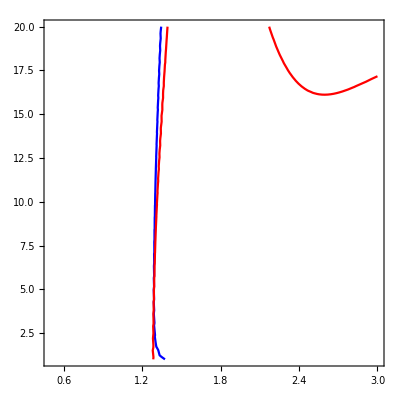

1.2896

4.70548

0.097914

-0.113369

```mathematica
g10s=g10mid*1.1;
ns=nmid*0.9;

lamdaf=v1lamdaf1;
beta=v1beta1;
h=v1h1;
KK=v1KK1;
phif=v1phif1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.15;
ninit=4.4;


sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];

ContourPlot[{CriticalCondition==0,dparital==0},{g10,0.5,3},{n,1,20},ContourStyle->{Blue,Red}]

inverse1g101=g10/. sol
inverse1n1=n/. sol

err1g101=(inverse1g101-g10s)/g10s;
err1n1=(inverse1n1-ns)/ns;

targetg10=(inverse1g101-g10mid)/g10mid
targetn=(inverse1n1-nmid)/nmid
```

```mathematica
Print[{PercentForm[(v1h1-hTarget)/hTarget,3],PercentForm[(v1KK1-KKTarget)/KKTarget,3],PercentForm[(v1beta1-betaTarget)/betaTarget,3],PercentForm[(v1lamdaf1-lamdafTarget)/lamdafTarget,3],PercentForm[(v1phif1-phifTarget)/phifTarget,3],PercentForm[targetg10,3],PercentForm[targetn,3]}]
```

{-4%,33.3%,-69.4%,-15.1%,-25%,9.79%,-11.3%}

### 1.2 Middle-aged group 20%

```mathematica
betaTarget=Pi/4;
lamdafTarget=0.93;
hTarget=0.01;
KKTarget=0.225;
phifTarget=0.8;
g10mid=1.1745935945603059;
nmid=5.307151031416191;


c0=1;g30=1;cf=100;phim=1-phif;
g12=1;
(*v1h1=0.014991744;
v1KK1=0.153417948;
v1beta1=0.738728456;
v1lamdaf1=0.7;
v1phif1=0.612584078;*)

v1h1=0.012;
v1KK1=0.25;
v1beta1=0.56;
v1lamdaf1=0.80;
v1phif1=0.69;
```

```mathematica
g10s=g10mid*1.2;
ns=nmid*0.8;

lamdaf=v1lamdaf1;
beta=v1beta1;
h=v1h1;
KK=v1KK1;
phif=v1phif1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.15;
ninit=4.4;


sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];

inverse1g101=g10/. sol;
inverse1n1=n/. sol;

err1g101=(inverse1g101-g10s)/g10s;
err1n1=(inverse1n1-ns)/ns;

targetg10=(inverse1g101-g10mid)/g10mid
targetn=(inverse1n1-nmid)/nmid
```

0.201286

-0.19392

```mathematica
Print[{PercentForm[(v1h1-hTarget)/hTarget,3],PercentForm[(v1KK1-KKTarget)/KKTarget,3],PercentForm[(v1beta1-betaTarget)/betaTarget,3],PercentForm[(v1lamdaf1-lamdafTarget)/lamdafTarget,3],PercentForm[(v1phif1-phifTarget)/phifTarget,3],PercentForm[targetg10,3],PercentForm[targetn,3]}]
```

{20%,11.1%,-28.7%,-14%,-13.8%,20.1%,-19.4%}

### 1.3 Elderly group 10%

```mathematica
betaTarget=Pi/8;
lamdafTarget=0.96;
hTarget=0.008;
KKTarget=0.175;
phifTarget=0.6;
g10older=1.0515238928342359;
nolder=4.730699457732493;

c0=1;g30=1;cf=100;phim=1-phif;
g12=1;

(*v1h1=0.007830847;
v1KK1=0.135282076537192;
v1beta1=0.119078242;
v1lamdaf1=0.9;
v1phif1=0.572040727;*)

v1h1=0.007830847;
v1KK1=0.135282076537192;
v1beta1=0.119078242;
v1lamdaf1=0.9;
v1phif1=0.572040727;
```

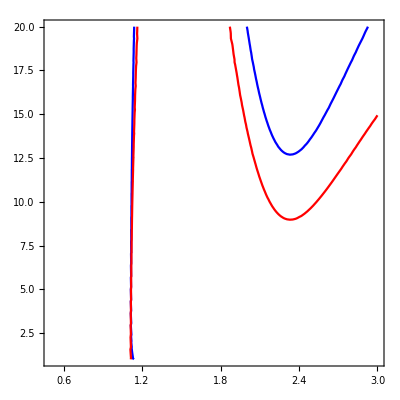

1.11416

4.30522

0.0595641

-0.0899409

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];

g10s=g10older*1.1;
ns=nolder*0.9;


lamdaf=v1lamdaf1;
beta=v1beta1;
h=v1h1;
KK=v1KK1;
phif=v1phif1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.15;
ninit=4.4;

ContourPlot[{CriticalCondition==0,dparital==0},{g10,0.5,3},{n,1,20},ContourStyle->{Blue,Red}]
sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];

inverse1g101=g10/. sol
inverse1n1=n/. sol

err1g101=(inverse1g101-g10s)/g10s;
err1n1=(inverse1n1-ns)/ns;

targetg10=(inverse1g101-g10older)/g10older
targetn=(inverse1n1-nolder)/nolder
```

```mathematica
Print[{PercentForm[(v1h1-hTarget)/hTarget,3],PercentForm[(v1KK1-KKTarget)/KKTarget,3],PercentForm[(v1beta1-betaTarget)/betaTarget,3],PercentForm[(v1lamdaf1-lamdafTarget)/lamdafTarget,3],PercentForm[(v1phif1-phifTarget)/phifTarget,3],PercentForm[targetg10,3],PercentForm[targetn,3]}]
```

{-2.11%,-22.7%,-69.7%,-6.25%,-4.66%,5.96%,-8.99%}

### 1.4 Elderly group 20%

```mathematica
betaTarget=Pi/8;
lamdafTarget=0.96;
hTarget=0.008;
KKTarget=0.175;
phifTarget=0.6;
g10older=1.0515238928342359;
nolder=4.730699457732493;


c0=1;g30=1;cf=100;phim=1-phif;
g12=1;
v1h1=0.011648498;
v1KK1=0.2186558;
v1beta1=0.396182259;
v1lamdaf1=0.832549613;
v1phif1=0.650163084253401;
```

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10older*1.2;
ns=nolder*0.8;





lamdaf=v1lamdaf1;
beta=v1beta1;
h=v1h1;
KK=v1KK1;
phif=v1phif1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.15;
ninit=4.4;


sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];

inverse1g101=g10/. sol;
inverse1n1=n/. sol;

err1g101=(inverse1g101-g10s)/g10s;
err1n1=(inverse1n1-ns)/ns;

targetg10=(inverse1g101-g10older)/g10older
targetn=(inverse1n1-nolder)/nolder
```

0.190561

-0.184866

```mathematica
Print[{PercentForm[(v1h1-hTarget)/hTarget,3],PercentForm[(v1KK1-KKTarget)/KKTarget,3],PercentForm[(v1beta1-betaTarget)/betaTarget,3],PercentForm[(v1lamdaf1-lamdafTarget)/lamdafTarget,3],PercentForm[(v1phif1-phifTarget)/phifTarget,3],PercentForm[targetg10,3],PercentForm[targetn,3]}]
```

{45.6%,24.9%,0.887%,-13.3%,8.36%,19.1%,-18.5%}

## Part II Small data

### 1.1 Middle-aged group 10%

```mathematica
betaTarget=Pi/4;
lamdafTarget=0.93;
hTarget=0.01;
KKTarget=0.225;
phifTarget=0.8;
g10mid=1.1745935945603059;
nmid=5.307151031416191;



c0=1;g30=1;cf=100;phim=1-phif;
g12=1;
(*v1h1=0.012192217;
v1KK1=0.212789861;
v1beta1=0.471238898;
v1lamdaf1=0.7;
v1phif1=0.78361723;*)

v1h1=0.0094;
v1KK1=0.22;
v1beta1=0.49;
v1lamdaf1=0.83;
v1phif1=0.67;
```

```mathematica
g10s=g10mid*1.1;
ns=nmid*0.9;

lamdaf=v1lamdaf1;
beta=v1beta1;
h=v1h1;
KK=v1KK1;
phif=v1phif1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.15;
ninit=4.4;


sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];

inverse1g101=g10/. sol;
inverse1n1=n/. sol;

err1g101=(inverse1g101-g10s)/g10s;
err1n1=(inverse1n1-ns)/ns;

targetg10=(inverse1g101-g10mid)/g10mid
targetn=(inverse1n1-nmid)/nmid
```

0.0983085

-0.107703

```mathematica
Print[{PercentForm[(v1h1-hTarget)/hTarget,3],PercentForm[(v1KK1-KKTarget)/KKTarget,3],PercentForm[(v1beta1-betaTarget)/betaTarget,3],PercentForm[(v1lamdaf1-lamdafTarget)/lamdafTarget,3],PercentForm[(v1phif1-phifTarget)/phifTarget,3],PercentForm[targetg10,3],PercentForm[targetn,3]}]
```

{-6%,-2.22%,-37.6%,-10.8%,-16.3%,9.83%,-10.8%}

### 1.2 Middle-aged group 20%

```mathematica
betaTarget=Pi/4;
lamdafTarget=0.93;
hTarget=0.01;
KKTarget=0.225;
phifTarget=0.8;
g10mid=1.1745935945603059;
nmid=5.307151031416191;


c0=1;g30=1;cf=100;phim=1-phif;
g12=1;
(*v1h1=0.015;
v1KK1=0.16537844;
v1beta1=0.631795362;
v1lamdaf1=0.718119783;
v1phif1=0.652396982;*)

v1h1=0.01;
v1KK1=0.24;
v1beta1=0.22;
v1lamdaf1=0.72;
v1phif1=0.67;
```

```mathematica
g10s=g10mid*1.2;
ns=nmid*0.8;

lamdaf=v1lamdaf1;
beta=v1beta1;
h=v1h1;
KK=v1KK1;
phif=v1phif1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.15;
ninit=4.4;


sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];

inverse1g101=g10/. sol;
inverse1n1=n/. sol;

err1g101=(inverse1g101-g10s)/g10s;
err1n1=(inverse1n1-ns)/ns;

targetg10=(inverse1g101-g10mid)/g10mid
targetn=(inverse1n1-nmid)/nmid
```

0.208362

-0.194955

```mathematica
Print[{PercentForm[(v1h1-hTarget)/hTarget,3],PercentForm[(v1KK1-KKTarget)/KKTarget,3],PercentForm[(v1beta1-betaTarget)/betaTarget,3],PercentForm[(v1lamdaf1-lamdafTarget)/lamdafTarget,3],PercentForm[(v1phif1-phifTarget)/phifTarget,3],PercentForm[targetg10,3],PercentForm[targetn,3]}]
```

{0%,6.67%,-72%,-22.6%,-16.3%,20.8%,-19.5%}

### 1.3 Elderly group 10%

```mathematica
betaTarget=Pi/8;
lamdafTarget=0.96;
hTarget=0.008;
KKTarget=0.175;
phifTarget=0.6;
g10older=1.0515238928342359;
nolder=4.730699457732493;


c0=1;g30=1;cf=100;phim=1-phif;
g12=1;
v1h1=0.009996701;
v1KK1=0.2;
v1beta1=0.471238898;
v1lamdaf1=0.895047851742281;
v1phif1=0.677972546147537;
```

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10older*1.1;
ns=nolder*0.9;





lamdaf=v1lamdaf1;
beta=v1beta1;
h=v1h1;
KK=v1KK1;
phif=v1phif1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.15;
ninit=4.4;


sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];

inverse1g101=g10/. sol;
inverse1n1=n/. sol;

err1g101=(inverse1g101-g10s)/g10s;
err1n1=(inverse1n1-ns)/ns;

targetg10=(inverse1g101-g10older)/g10older
targetn=(inverse1n1-nolder)/nolder
```

0.100757

-0.100058

```mathematica
Print[{PercentForm[(v1h1-hTarget)/hTarget,3],PercentForm[(v1KK1-KKTarget)/KKTarget,3],PercentForm[(v1beta1-betaTarget)/betaTarget,3],PercentForm[(v1lamdaf1-lamdafTarget)/lamdafTarget,3],PercentForm[(v1phif1-phifTarget)/phifTarget,3],PercentForm[targetg10,3],PercentForm[targetn,3]}]
```

{25%,14.3%,20%,-6.77%,13%,10.1%,-10%}

### 1.4 Elderly group 20%

```mathematica
betaTarget=Pi/8;
lamdafTarget=0.96;
hTarget=0.008;
KKTarget=0.175;
phifTarget=0.6;
g10older=1.0515238928342359;
nolder=4.730699457732493;


c0=1;g30=1;cf=100;phim=1-phif;
g12=1;
(*v1h1=0.012120131;
v1KK1=0.297037256;
v1beta1=0.156282082;
v1lamdaf1=0.800739544;
v1phif1=0.65;*)

v1h1=0.012;
v1KK1=0.30;
v1beta1=0.16;
v1lamdaf1=0.8;
v1phif1=0.65;
```

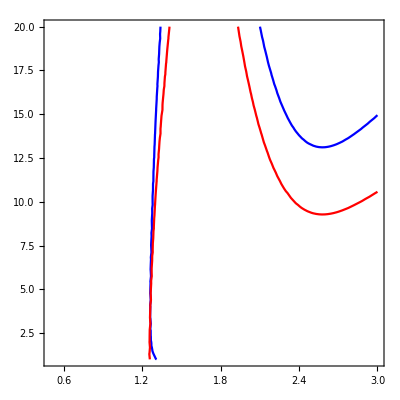

1.26199

3.82374

0.200153

-0.191719

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10older*1.2;
ns=nolder*0.8;





lamdaf=v1lamdaf1;
beta=v1beta1;
h=v1h1;
KK=v1KK1;
phif=v1phif1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.3;
ninit=4.4;

ContourPlot[{CriticalCondition==0,dparital==0},{g10,0.5,3},{n,1,20},ContourStyle->{Blue,Red}]
sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];

inverse1g101=g10/. sol
inverse1n1=n/. sol

err1g101=(inverse1g101-g10s)/g10s;
err1n1=(inverse1n1-ns)/ns;

targetg10=(inverse1g101-g10older)/g10older
targetn=(inverse1n1-nolder)/nolder
```

```mathematica
Print[{PercentForm[(v1h1-hTarget)/hTarget,3],PercentForm[(v1KK1-KKTarget)/KKTarget,3],PercentForm[(v1beta1-betaTarget)/betaTarget,3],PercentForm[(v1lamdaf1-lamdafTarget)/lamdafTarget,3],PercentForm[(v1phif1-phifTarget)/phifTarget,3],PercentForm[targetg10,3],PercentForm[targetn,3]}]
```

{50%,71.4%,-59.3%,-16.7%,8.33%,20%,-19.2%}